### Lotka Volterra Dynamics

Here are the growth rate and interactions parameters for the LV

```mathematica
r1=1;a11=1.3;a12=-2;
r2=-1.1;a21=2.2;a22=-1.5;
```

Here the self interaction terms are chosen appropriately to yield the following equations

```mathematica
{Subscript[y, 1]'[t]==Subscript[y, 1][t](r1+a11 Subscript[y, 1][t]+a12 Subscript[y, 2][t]),
Subscript[y, 2]'[t]==Subscript[y, 2][t](a21 Subscript[y, 1][t]+a22 Subscript[y, 2][t]+r2)}
```

{y_1'[t]==y_1[t] (1+1.3 y_1[t]-2 y_2[t]),y_2'[t]==(-1.1+2.2 y_1[t]-1.5 y_2[t]) y_2[t]}

```mathematica
predprey=NDSolve[{
Subscript[y, 1]'[t]==Subscript[y, 1][t](r1+a11 Subscript[y, 1][t]+a12 Subscript[y, 2][t]),
Subscript[y, 2]'[t]==Subscript[y, 2][t](a21 Subscript[y, 1][t]+a22 Subscript[y, 2][t]+r2),
Subscript[y, 1][0]==0.2,Subscript[y, 2][0]==0.5},{Subscript[y, 1],Subscript[y, 2]},{t,0,100,0.1}]
```

{{y_1→InterpolatingFunction[…],y_2→InterpolatingFunction[…]}}

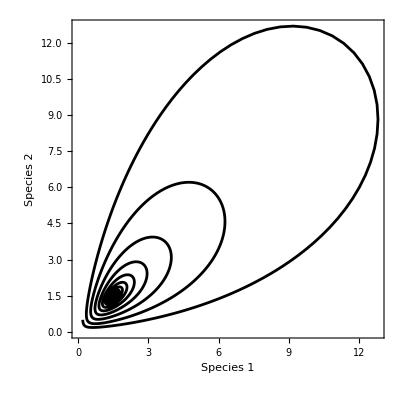

```mathematica
ListPlot[Table[Evaluate[{Subscript[y, 1][t],Subscript[y, 2][t]}/.predprey]⟦1⟧,{t,0,100,0.005}],Joined->True,Axes->None,PlotStyle->Black,PlotStyle->Black,PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],PlotRange->Full,FrameLabel->{Style["Species 1",16,RGBColor["#807FFF"]],Style["Species 2",16,RGBColor["#DEAD26"]]},AspectRatio->1]
```

## Equivalent replicator dynamics

### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

### Plotting

For  the  two player case

```mathematica
twoplpayoffs={{a11,a12,r1},{a21,a22,r2},{0,0,0}};
fits[x_,y_]:=twoplpayoffs.{x,y,1-x-y};
```

```mathematica
π1[x_,y_,z_]:=fits[x,y]⟦1⟧;

π2[x_,y_,z_]:=fits[x,y]⟦2⟧;

π3[x_,y_,z_]:=fits[x,y]⟦3⟧;
πbar[x_,y_,z_]:=x π1[x,y,z]+y π2[x,y,z]+z π3[x,y,z];
dx[x_, y_, z_]:=x(π1[x,y,z]-πbar[x,y,z]);
dy[x_, y_, z_]:=y(π2[x,y,z]-πbar[x,y,z]);
dz[x_, y_, z_]:=z(π3[x,y,z]-πbar[x,y,z]);

Fermi[x_]:={
dx[x⟦1⟧,x⟦2⟧, x⟦3⟧],
dy[x⟦1⟧,x⟦2⟧, x⟦3⟧],
dz[x⟦1⟧,x⟦2⟧, x⟦3⟧]
}
x=.;y=.;z=1-x-y;
fa=fits[x,y]⟦1⟧;
fb=fits[x,y]⟦2⟧;
fc=fits[x,y]⟦3⟧;
```

```mathematica
x=.
y=.
PT//MatrixForm;
sol=NSolve[{dx[x,y,1-x-y]==0,dy[x,y,1-x-y]==0},{x,y},Reals];
```

```mathematica
data={x,y}/.sol;
relData=Select[data,Total[#]<=1&&Total[#]≥0&];
p1=ListPlot[relData,PlotStyle->{Black,PointSize[0.03]}];
p2=ListPlot[relData,PlotStyle->{White,PointSize[0.015]}];
p3=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{Red,PointSize[0.03]}];
p4=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{White,PointSize[0.015]}];
points=Show[p1,p2,p3,p4];
```

Plotting  isoclines

```mathematica
eq1=fa-fc;
eq2=fb-fc;
```

```mathematica
cplt=ContourPlot[eq1==0,{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y≤1],PlotRange->All,ContourStyle->Darker[Red]];
cplt2=ContourPlot[eq2==0,{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y≤1],PlotRange->All,ContourStyle->Darker[Blue]];
```

```mathematica
sp=StreamDensityPlot[{dx[x,y,1-x-y],dy[x,y,1-x-y]},{x,0,1},{y,0,1},Frame->True,ColorFunction->"Pastel",ColorFunctionScaling->False,StreamStyle->Darker[Gray],StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,RegionFunction->Function[{x,y,vx,vy,n},x +y≤1&&x≥0&&y≥0]];
```

```mathematica
trajdata=NDSolve[{x'[t]==dx[x[t],y[t],1-x[t]-y[t]],y'[t]==dy[x[t],y[t],1-x[t]-y[t]],x[0]==0.45,y[0]==0.08},{x,y},{t,0,50}];
parpl=ParametricPlot[Evaluate[{x[t],y[t]}/.trajdata],{t,0,50},PlotRange->All,PlotStyle->Directive[Black,Dashed]];
```

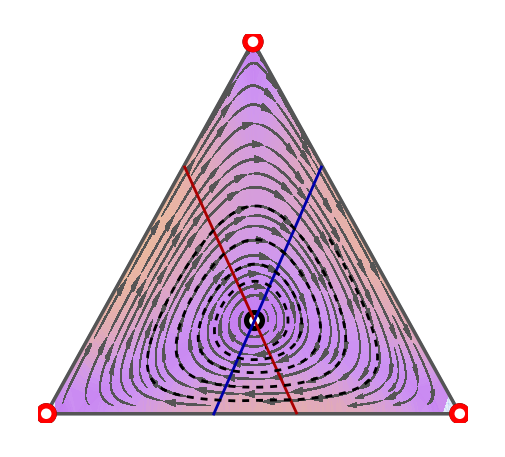

```mathematica
psim=Show[
Graphics[GeometricTransformation[First[Show[sp]],trans]],triangle,Graphics[GeometricTransformation[First[Show[points]],trans]],
Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],
Graphics[GeometricTransformation[First[parpl],trans]](*,
Graphics[GeometricTransformation[Text["label",{0,1}],trans]]*)
]
```